## Change in soil quality and the cumulative soil quality for a set sequence

```mathematica
allcash=ConstantArray[-1,50];
allcover=ConstantArray[1,50];
```

```mathematica
setseq={1,1,1,-1,1,-1,1,1,-1,1,-1,-1,-1,1,-1,-1,-1,1,-1,1,-1,1,-1,-1,1,-1,-1,1,1,1,-1,-1,-1,1,1,1,1,1,-1,-1,-1,1,1,1,1,1,-1,-1,1,-1};
```

```mathematica
seq=setseq;
accsoil=Accumulate[seq];
```

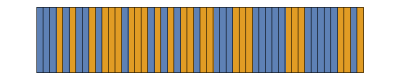

```mathematica
gold=RGBColor["#FFD700"];
{covercol,cashcol}=ColorData[97,"ColorList"]⟦{1,2}⟧(*{Purple,gold}*);
ArrayPlot[{seq},ColorRules->{1->covercol,-1->cashcol},Mesh->True,MeshStyle->Directive[Black,Thickness[0.001]]]
```

```mathematica
ColorData[97,"ColorList"]⟦{1,2}⟧
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051]}

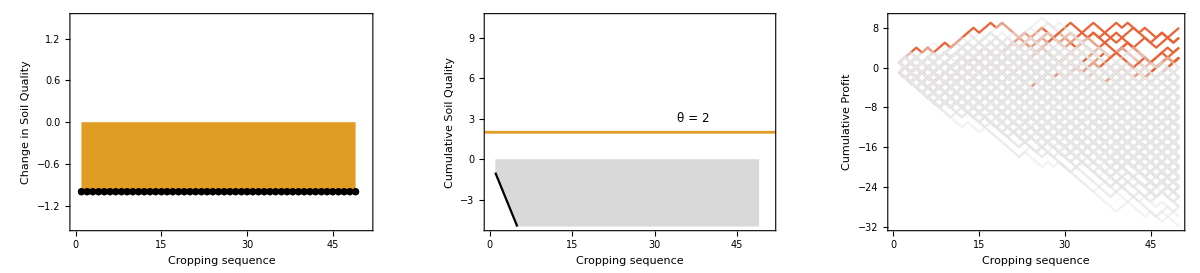

```mathematica
GraphicsRow[{ListPlot[seq⟦1;;Length[seq]-1⟧,PlotRange->{{0,51},{-1.5,1.5}},Frame->True,Joined->True,FrameStyle->{Black,Thickness[0.002]},AxesOrigin->{1,0},PlotStyle->Directive[Black,Thickness[0.007]],
FrameLabel->{Style["Cropping sequence",14,Black],Style["Change in Soil Quality",14,Black]},Mesh->Full,Filling->{1->{Axis,{cashcol,covercol}}}],
ListPlot[accsoil⟦1;;Length[seq]-1⟧,PlotRange->{{0,51},{-5,10.5}},PlotStyle->Black,Frame->True,Joined->True,FrameStyle->{Black,Thickness[0.001]},
FrameLabel->{Style["Cropping sequence",14,Black],Style["Cumulative Soil Quality",14,Black]},Filling->{1->{Axis,LightGray}},GridLines->{None,{2}},GridLinesStyle->Directive[cashcol,Thickness[0.005]],Method->{"GridLinesInFront"->True},Epilog->Inset[Style["θ = 2",12],{37,3}]],profits},ImageSize->Full]
```

```mathematica
(*Export["/Users/gokhale/Desktop/sq.mov",Table[ListPlot[seq⟦1;;i-1⟧,PlotRange->{{0,51},{-1.5,1.5}},Frame->True,Joined->True,FrameStyle->{Black,Thickness[0.002]},AxesOrigin->{1,0},PlotStyle->Directive[Black,Thickness[0.007]],
FrameLabel->{Style["Cropping sequence",14,Black],Style["Change in Soil Quality",14,Black]},Mesh->Full,Filling->{1->{Axis,{cashcol,covercol}}}],{i,2,Length[seq],1}],FrameRate->5]*)
```

/Users/gokhale/Desktop/Untitled.mov

```mathematica
(*Export["/Users/gokhale/Desktop/cumusq.mov",Table[ListPlot[accsoil⟦1;;i-1⟧,PlotRange->{{0,51},{-5,10.5}},PlotStyle->Black,Frame->True,Joined->True,FrameStyle->{Black,Thickness[0.001]},
FrameLabel->{Style["Cropping sequence",14,Black],Style["Cumulative Soil Quality",14,Black]},Filling->{1->{Axis,LightGray}},GridLines->{None,{2}},GridLinesStyle->Directive[cashcol,Thickness[0.005]],Method->{"GridLinesInFront"->True},Epilog->Inset[Style["θ = 2",12],{37,3}]],{i,2,Length[seq],1}],FrameRate->5]*)
```

/Users/gokhale/Desktop/cumusq.mov

## Simulating trajectories for cumulative profit

```mathematica
numberofsimulations=1000;

p=0.2;
p1=0.5;
p2=0.9;
profit=seq/.{1->-1,-1->1};
createtrajectories[maxruns_]:=Module[{max=maxruns},
runs={};
For[numerofruns=1,numerofruns≤max,numerofruns++,
trajectory={};
For[i=1,i≤Length[profit],i++,
If[profit⟦i⟧==-1,AppendTo[trajectory,If[RandomReal[]<p,1,-1]]];
If[profit⟦i⟧==1,AppendTo[trajectory,If[accsoil⟦i⟧>2,If[RandomReal[]<p2,1,-1],If[RandomReal[]<p1,1,-1]]]];
];
AppendTo[runs,Accumulate[trajectory]]
]
]
```

```mathematica
createtrajectories[numberofsimulations]
```

```mathematica
won=0;
If[#>0,won++]&/@runs⟦All,Length[seq]⟧;
```

```mathematica
colorscheme=If[#>0,ColorData[97,"ColorList"]⟦{4}⟧,Directive[GrayLevel[0.9],Opacity[0.5]]]&/@runs⟦All,50⟧;
profits=ListPlot[runs,Joined->True,PlotStyle->colorscheme,Frame->True,FrameStyle->{Black,Thickness[0.002]},
FrameLabel->{Style["Cropping sequence",14,Black],Style["Cumulative Profit",14,Black]},Background->White];
pie=PieChart[{won/numberofsimulations//N,1-won/numberofsimulations//N},ChartStyle->Flatten[{ColorData[97,"ColorList"]⟦{4}⟧,GrayLevel[0.82]}],ChartLegends->{"Profit making trajectories","Trajectories incurring loss"}];
```

```mathematica
numberofsimulations-won
```

992

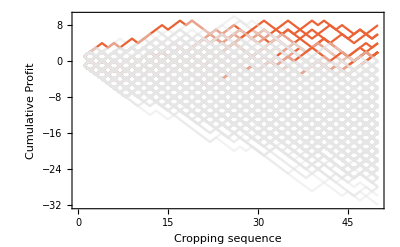

```mathematica
GraphicsRow[{profits,pie},ImageSize->Full]
```

```mathematica
(*Export["/Users/gokhale/Desktop/profits.mov",Table[ListPlot[runs⟦All,1;;i⟧,Joined->True,PlotStyle->colorscheme,Frame->True,FrameStyle->{Black,Thickness[0.002]},
FrameLabel->{Style["Cropping sequence",14,Black],Style["Cumulative Profit",14,Black]},Background->White,PlotRange->{{-0.1,50.1},{-41,12}}],{i,2,50,1}],FrameRate->5]*)
```